# Waves: Complete Edition

Mohammad H.Sadeghzadeh
Department of Physics, Faculty of Science, Ferdowsi University of Mashhad
Yousef Sadeghi
Department of Physics, Faculty of Science, Ferdowsi University of Mashhad

I.  INTRODUCTION

In physics, a wave is a propagating dynamic disturbance (change from equilibrium) of one or more quantities, sometimes as described by a wave equation. In physical waves, at least two field quantities in the wave medium are involved. Waves can be periodic, in which case those quantities oscillate repeatedly about an equilibrium (resting) value at some frequency. When the entire waveform moves in one direction it is said to be a traveling wave; by contrast, a pair of superimposed periodic waves traveling in opposite directions make a standing wave.
Mechanical waves are one of the most commonly studied types of waves in classical physics. In a mechanical wave, stress and strain fields oscillate about a mechanical equilibrium. A mechanical wave is a local deformation (strain) in some physical medium that propagates from particle to particle by creating local stresses that cause strain in neighboring particles too. For example, sound waves are variations of the local pressure and particle motion that propagate through the medium. Other examples of mechanical waves are seismic waves, surface waves, and string vibrations (standing waves).^1
In this program, using four different methods we simulate the behavior of sound waves in different situations with spherical wave equation.^2

II.  N-SOURCE SIMULATION
The program makes n-sources in a vertical line which are all perfectly coherent and takes the sum of them, the resulting wave function is then assigned to function “ψ”.
Every variable can be changed by the user but for the best results only make changes in the specified range.

A.  First Method: DensityPlot
In this method we use DensityPlot to simulate spherical waves.

1.  Two-Dimensional Space

```mathematica
ν:=500(*frequency -> (20 - 2000)*)
ψmax:=1(*amplitude -> (0 - 1)*)
n:=2(*number of sources -> (1 - 10)*)
d:=1(*distance between sources -> (0 - 20)*)
v:=343(*phase velocity, constant, change at your own risk!*)
ω:=2*π*ν(*angular frequency*)
k:=ω/v(*wave number*)
T:=1/ν(*time period*)
λ:=v/ν(*wave length*)
lst:={}
Do[AppendTo[lst,ψmax/Sqrt[x^2+(y-i*d)^2] *Sin[k*Sqrt[x^2+(y-i*d)^2]-ω*t]],{i,1,n}](*this loop creates n sources which have d units distance from each other on a vertical line*)
ψ[x_,y_,t_]=Total[lst];
Manipulate[DensityPlot[ψ[x,y,t] ,{x,0,d*(n+1)+5*λ},{y,0,d*(n+1)},PlotPoints->100,PlotLegends->BarLegend[Automatic,LegendMarkerSize->300,LegendFunction->"Frame",LegendMargins->10,LegendLabel->"Height"],Background->White],{t,0,10*T}]
```

2.  Three-Dimensional Space

```mathematica
ν:=500(*frequency -> (20 - 1000)*)
ψmax:=1(*amplitude -> (0 - 1)*)
d:=2(*distance between sources -> (0 - 20)*)
v:=343(*phase velocity, constant, change at your own risk!*)
ω:=2*π*ν(*angular frequency*)
k:=ω/v(*wave number*)
T:=1/ν(*time period*)
λ:=v/ν(*wave length*)
ψ01[x_,y_,z_,t_]:=ψmax/Sqrt[x^2+(y-d/2)^2+z^2]*Sin[k*Sqrt[x^2+(y-d/2)^2+z^2]-ω*t]
ψ02[x_,y_,z_,t_]:=ψmax/Sqrt[x^2+(y+d/2)^2+z^2]*Sin[k*Sqrt[x^2+(y+d/2)^2+z^2]-ω*t]
ψ[x_,y_,z_,t_]:=ψ01[x,y,z,t]+ψ02[x,y,z,t]
Manipulate[DensityPlot3D[ψ[x,y,z,t] ,{x,-d*(n+1),d*(n+1)},{y,-d*(n+1),d*(n+1)},{z,-d*(n+1),d*(n+1)},PlotPoints->50,AxesLabel->Automatic,Background->White],{t,0,10*T}]
```

B.  Second Method: ContourPlot
In this method we use ContourPlot to simulate spherical waves.

```mathematica
ν:=500(*frequency -> (20 - 2000)*)
ψmax:=1(*amplitude -> (0 - 1)*)
n:=2(*number of sources -> (1 - 10)*)
d:=1(*distance between sources -> (0 - 20)*)
v:=343(*phase velocity, constant, change at your own risk!*)
ω:=2*π*ν(*angular frequency*)
k:=ω/v(*wave number*)
T:=1/ν(*time period*)
λ:=v/ν(*wave length*)
lst:={}
Do[AppendTo[lst,ψmax/Sqrt[x^2+(y-i*d)^2] *Sin[k*Sqrt[x^2+(y-i*d)^2]-ω*t]],{i,1,n}](*this loop creates n sources which have d units distance from each other on a vertical line*)
ψ[x_,y_,t_]=Total[lst];
Manipulate[ContourPlot[ψ[x,y,t],{x,0,d*(n+1)+5*λ},{y,0,d*(n+1)},ContourLines->False,Contours->50,PlotLegends->BarLegend[Automatic,LegendMarkerSize->300,LegendFunction->"Frame",LegendMargins->10,LegendLabel->"Height"]],{t,0,10*T}]
```

C.  Third Method: Plot3D
In this method we use Plot3D to simulate spherical waves.

```mathematica
ν:=500(*frequency -> (20 - 2000)*)
ψmax:=1(*amplitude -> (0 - 1)*)
d:=2(*distance between sources -> (0 - 20)*)
v:=343(*phase velocity, constant, change at your own risk!*)
ω:=2*π*ν(*angular frequency*)
k:=ω/v(*wave number*)
T:=1/ν(*time period*)
λ:=v/ν(*wave length*)
ψ01[x_,y_,t_]:=ψmax/Sqrt[x^2+(y-d/2)^2]*Sin[k*Sqrt[x^2+(y-d/2)^2]-ω*t]
ψ02[x_,y_,t_]:=ψmax/Sqrt[x^2+(y+d/2)^2]*Sin[k*Sqrt[x^2+(y+d/2)^2]-ω*t]
ψ[x_,y_,t_]:=ψ01[x,y,t]+ψ02[x,y,t]
Manipulate[Plot3D[ψ[x,y,t],{x,-5*d-10*λ,5*d+10*λ},{y,-5*d-10*λ,5*d+10*λ},PlotPoints->100,AxesLabel->Automatic,Background->White],{t,0,10*T}]
```

D.  Fourth Method: RegionPlot
In this method we use RegionPlot to simulate spherical waves.

```mathematica
ν:=500(*frequency -> (20 - 2000)*)
ψmax:=1(*amplitude -> (0 - 1)*)
n:=2(*number of sources -> (1 - 10)*)
d:=2(*distance between sources -> (0 - 20)*)
v:=343(*phase velocity, constant, change at your own risk!*)
ω:=2*π*ν(*angular frequency*)
k:=ω/v(*wave number*)
T:=1/ν(*time period*)
λ:=v/ν(*wave length*)
lst:={}
Do[AppendTo[lst,ψmax/Sqrt[x^2+(y-i*d)^2] *Sin[k*Sqrt[x^2+(y-i*d)^2]-ω*t]],{i,1,n}](*this loop creates n sources which have d units distance from each other on a vertical line*)
ψ[x_,y_,t_]=Total[lst];
Manipulate[RegionPlot[ψ[x,y,t]≤ 0,{x,0,d*(n+1)+5*λ},{y,0,d*(n+1)},PlotPoints->100,Background->White],{t,0,10*T}]
```

III.  RESULTS AND ANALYSIS
As can be seen the program has the ability to simulate any amount of sources in different ways, we have simulated one to five sources in different situations below:

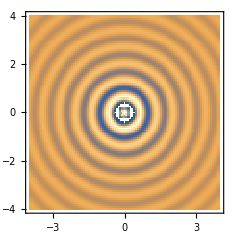
A.  One-Source Model
As can be seen above if we let n be 1, we can visualize the behavior of sound waves from one source.
 
-Graphics-

Figure 1.  Light parts show wave crests and dark parts show wave troughs, made using DensityPlot.

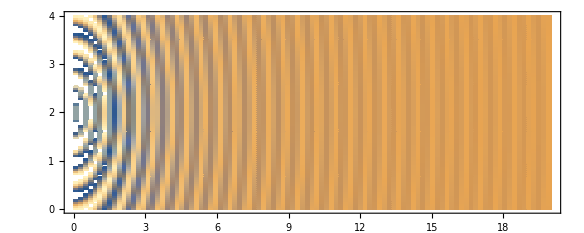

Figure 2.  Wave-fronts at far distances come out of circular shape and become straight lines, made using DensityPlot.

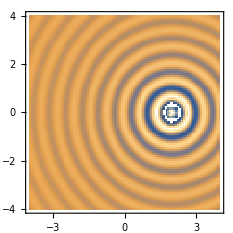
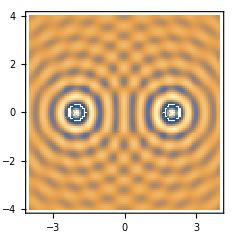
B.  Two-Source Model
Now if we add another source to the simulation we can visualize the behavior of sound waves from two perfectly coherent sources.

-Graphics- -Graphics-

Figure 3.  At point (0,0) where 2 waves meet a standing wave is created. This happens because when a pair of superimposed periodic waves traveling in opposite directions make a standing wave, made using DensityPlot.

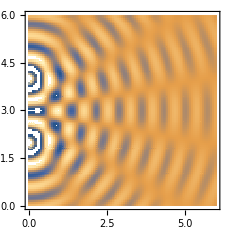

Figure 4.  Two sources interfering in 2D, made using DensityPlot.

-Graphics3D- -Graphics3D-

Figure 5.  Two sources interfering in 3D, made using DensityPlot3D.

-Graphics- -Graphics-

Figure 6.  Two sources interfering in 3D, made using Plot3D.

Multiple sources interfere with each other as shown in the above figures, for 2-sources this results in a hyperbola.

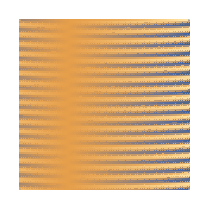
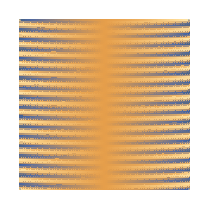
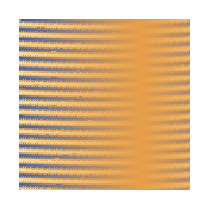

Figure 7.  If we observe the behavior of waves at long distances where interference happens we can visualize how waves oscillate air particles as shown in the above figure, made using DensityPlot.

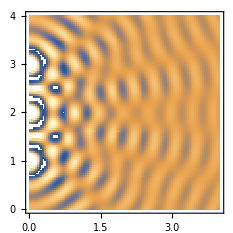
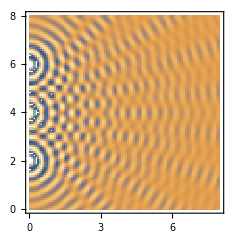
C.  Three-Source Model
If we add another source to the simulation we can visualize the behavior of sound waves from three perfectly coherent sources.

-Graphics- -Graphics-

Figure 8.  Interference due to three sources in a vertical line, made using DensityPlot.

-Graphics- -Graphics-

Figure 9.  Interference due to three sources in a equilateral triangle’s corners, 4 meters length (left) and λ meters length (right), made using DensityPlot.

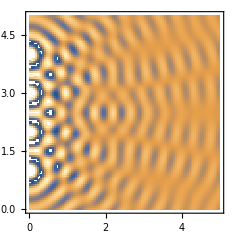
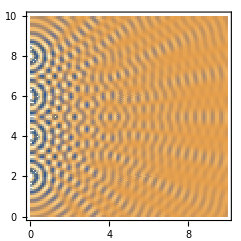
D.  Four-Source Model
We can add another source to simulate the behavior of sound waves from four perfectly coherent sources.
 
-Graphics- -Graphics-

Figure 10.  Interference due to four sources in a vertical line, made using DensityPlot.

-Graphics- -Graphics-

Figure 11.  Interference due to four sources in a square’s corners, 1 meters length (left) and λ meters length (right), made using DensityPlot.

E.  Five-Source Model
Finally, by adding another source we can simulate the behavior of sound waves from five perfectly coherent sources.
 
-Graphics- -Graphics-

Figure 12.  Interference due to five sources in a vertical line, made using DensityPlot.

IV.  GRAPHICAL INTERCHANGE FORMAT
Mathematica can’t show these animations correctly therefore in this section we try to pre-render the animations and then export them into “GIF” formats, this allows us to have smoother animations.
Due to the speed and frequency of the sound being very high, for making simulations they have to be set to ideal values.

A.  One-Source Model
This section is for creating GIFs that simulate waves from one source, for best results make changes only in the specified range.

1.  Two-Dimensional Space
This section is for creating GIFs that simulate waves from one source in 2D using DensityPlot, for best results make changes only in the specified range.

```mathematica
ν:=10(*frequency -> (1 - 10)*)
ψmax:=1(*amplitude -> (0 - 1)*)
v:=5(*phase velocity, constant, change at your own risk!*)
T:=1/ν(*time period*)
ω:=2*π*ν(*angular frequency*)
k:=ω/v(*wave number*)
λ:=v/ν(*wave length*)
ψ[x_,y_,t_]:=ψmax/Sqrt[x^2+y^2]*Sin[k*Sqrt[x^2+y^2]-ω*t](*wave function*)
lst:={}
time:=Range[0,10*T,(10*T)/100]
Do[AppendTo[lst,DensityPlot[ψ[x,y,t],{x,-10*λ,10*λ},{y,-10*λ,10*λ},PlotPoints->100]],{t,time}]
file:="WCE(1-source 2D).gif"
Export[file,lst];
```

2.  Three-Dimensional Space
This section is for creating GIFs that simulate waves from one source in 3D using Plot3D, for best results make changes only in the specified range.

```mathematica
ν:=10(* frequency -> (0 , 10)*)
ψmax:=1(* amplitude -> (0 , 1)*)
v:=5(*phase velocity, constant, change at your own risk!*)
T:=1/ν(*time period*)
ω:=2*π*ν(*angular frequency*)
k:=ω/v(*wave number*)
λ:=v/ν(*wave length*)
ψ[x_,y_,t_]:=ψmax/Sqrt[(x)^2+(y)^2]*Sin[k*Sqrt[(x)^2+(y)^2]-ω*t](*wave function*)
lst:={}
time:=Range[0,10*T,(10*T)/100]
Do[AppendTo[lst,Plot3D[ψ03[x,y,t],{x,-5*λ,5*λ},{y,-5*λ,5*λ},PlotRange->{{-5*λ,5*λ},{-5*λ,5*λ}},PlotPoints->100,ViewPoint->Above (*point of view in 3D*)]],{t,time}]
file:="WCE(1-source 3D).gif"
Export[file,lst];
```

B.  Two-Source Model
This section is for creating GIFs that simulate waves from two perfectly coherent sources, for best results make changes only in the specified range.

1.  Two-Dimensional Space
This section is for creating GIFs that simulate waves from two perfectly coherent sources in 2D using DensityPlot, for best results make changes only in the specified range.

```mathematica
ν:=10(* frequency -> (1 , 10)*)
ψmax:=1(* amplitude -> (0 , 1)*)
dx:=3(* distance between two sources on a horizontal line -> (0 , 10)*)
v:=5(*phase velocity, constant, change at your own risk!*)
T:=1/ν(*time period*)
ω:=2*π*ν(*angular frequency*)
k:=ω/v(*wave number*)
λ:=v/ν(*wave length*)
ψ01[x_,y_,t_]:=ψmax/Sqrt[(x-dx/2)^2+y^2]*Sin[k*Sqrt[(x-dx/2)^2+y^2]-ω*t](*first wave function*)
ψ02[x_,y_,t_]:=ψmax/Sqrt[(x+dx/2)^2+y^2]*Sin[k*Sqrt[(x+dx/2)^2+y^2]-ω*t](*second wave function*)
lst:={}
time:=Range[0,10*T,(10*T)/100]
Do[AppendTo[lst,DensityPlot[ψ01[x,y,t]+ψ02[x,y,t],{x,-dx,dx},{y,-dx,dx},PlotPoints->100]],{t,time}]
file:="WCE(2-source 2D).gif"
Export[file,lst];
```

2.  Three-Dimensional Space
This section is for creating GIFs that simulate waves from two perfectly coherent sources in 3D using Plot3D, for best results make changes only in the specified range.

```mathematica
ν:=10(* frequency -> (1 , 10)*)
ψmax:=1(* amplitude -> (0 , 1)*)
dy:=2(* distance between two sources -> (0 , 10)*)
v:=5(*phase velocity, constant, change at your own risk!*)
T:=1/ν(*time period*)
ω:=2*π*ν(*angular frequency*)
k:=ω/v(*wave number*)
λ:=v/ν(*wave length*)
ψ01[x_,y_,t_]:=ψmax/Sqrt[(x)^2+(y-dy/2)^2]*Sin[k*Sqrt[(x)^2+(y-dy/2)^2]-ω*t](*first wave function*)
ψ02[x_,y_,t_]:=ψmax/Sqrt[(x)^2+(y+dy/2)^2]*Sin[k*Sqrt[(x)^2+(y+dy/2)^2]-ω*t](*second wave function*)
lst:={}
time:=Range[0,10*T,(10*T)/100]
Do[AppendTo[lst,Plot3D[ψ01[x,y,t]+ψ02[x,y,t],{x,-5*λ,5*λ},{y,-5*λ,5*λ},PlotRange->{{-5*λ,5*λ},{-5*λ,5*λ}},PlotPoints->100,ViewPoint->Above(*point of view in 3D*)]],{t,time}]
file:="WCE(2-source 3D).gif"
Export[file,lst];
```

V.  CONCLUSION
In conclusion, it can be said the behaviour of sound waves was successfully simulated. As we saw wave interference changes with different amounts of sources and locus of these sources, for example, 2 sources interfering make hyperbola. In this simulation we used 4 deferent methods: DensityPlot, ContourPlot, Plot3D and  RegionPlot, each one had their own benefits, for showing preliminary results RegionPlot works best and for quality DensityPlot is best. Plot3D can also be used to show oscillation of air particles.

VI.  REFERENCE
1.  Halliday, David; Resnick, Robert; Walker, Jearl (2011). Fundamentals of Physics (9th ed.). John Wiley & Sons. ISBN 978-470-56158-4
2.  Wave - Wikipedia
      Viewed at: https://en.wikipedia.org/wiki/Wave
3.  Wave Interference - https://phet.colorado.edu/en/simulation/wave-interference
4.  Sound - https://phet.colorado.edu/en/simulation/legacy/sound
5.  Sound - Wikipedia
      Viewed at: https://en.wikipedia.org/wiki/Sound

VII.  AUTHOR CONTRIBUTIONS
M.H.S. realized the core idea for simulating waves, conceived the project, and wrote an initial program. Y.S. expanded on the main idea and contributed expertise towards programming. All authors participated in analyzing the results and revising the final manuscript.

VIII.  COMPETING INTRESETS
The authors declare no competing interests.